```mathematica
3-mode Transducer Coupling
```

```mathematica
Shoumik Chowdhury  7/8/2020
```

## Preliminaries

```mathematica
Id[n_]:=IdentityMatrix[n]
mJn[n_]:=ArrayFlatten[Id[n]⊗({{0, 1}, {-1, 0}})](*Symplectic matrix in QP basis*)
mJqqn[n_]:=ArrayFlatten[({{0, 1}, {-1, 0}})⊗Id[n]](*Symplectic matrix in QQ basis*)
sympQn[mS_,n_]:=1-Norm[mSᵀ.mJn[n].mS-mJn[n]](*Test for symplecticity*)
n=6;(*For a 3-mode transducer we work with n=6*)
mJ=mJn[n];
sympQ[mS_]:=sympQn[mS,n]
```

```mathematica
QQtoQP[n0_, M0_] :=
(* Converts a matrix from QQ basis to QP basis*) 
Module[{n=n0, M=M0},
	ord= Flatten[Table[{i, n+i}, {i, 1, n}]];
	Return[M⟦ord, ord⟧]
]

QPtoQQ[n0_, M0_] := 
(* Converts a matrix from QP basis to QQ basis*)
Module[{n=n0, M=M0},
	odds = Table[{i}, {i, 1, 2n, 2}];
	evens = Table[{i+1}, {i, 1, 2n, 2}];
	ord = Flatten[Join[odds,evens]];
	Return[M⟦ord, ord⟧]
] 

(*Generate random n×n symplectic matrix in QQ basis and convert to QP*)
rSymMat[{a_,b_},c_]:=(UpperTriangularize[#]+UpperTriangularize[#,1]ᵀ)&@RandomReal[{a,b},{c,c}];
rSympMat[a_,b_, n_]:=QQtoQP[n, Id[2n]-Inverse[(mJqqn[n].rSymMat[{a,b},2n]+1/2 Id[2n])]]; 
(*Generate random local operations for n = 6*)
randomLocal[a_, b_] := ArrayFlatten[({{rSympMat[a,b, 1], 0, 0, 0, 0, 0}, {0, rSympMat[a,b, 1], 0, 0, 0, 0}, {0, 0, rSympMat[a,b, 1], 0, 0, 0}, {0, 0, 0, rSympMat[a,b, 1], 0, 0}, {0, 0, 0, 0, rSympMat[a,b, 1], 0}, {0, 0, 0, 0, 0, rSympMat[a,b, 1]}})];
```

## Theory

References:"Cavity Optomechanics" (https: //arxiv.org/abs/1303.0733) and KL paper (https: //www.nature.com/articles/nphys2911)
Hamiltonian given by   (a⃗)^†.H.a⃗, where  a⃗ = {a_o, a_m, a_μ, a_o^†, a_m^†, a_μ^†} and  (a⃗)^†= {(a_o)^†,(a_m)^†,(a_μ)^†,a_o,a_m,a_μ}
H = 1/2(Δ_o | g_om | 0 | 0 | g_om | 0
g_om | ω_m | g_μm | g_om | 0 | g_μm
0 | g_μm | Δ_μ | 0 | g_μm | 0
0 | g_om | 0 | Δ_o | g_om | 0
g_om | 0 | g_μm | g_om | ω_m | g_μm
0 | g_μm | 0 | 0 | g_μm | Δ_μ) := (A | B
B^† | P)
Linearized Hamiltonian:H=Δ_o ((a_o)^† a_o+1/2)+Δ_μ ((a_μ)^† a_μ+1/2)+ω_m ((a_m)^† a_m+1/2)+g_om (a_o+(a_o)^†) (a_m+(a_m)^†)+g_μm (a_μ+(a_μ)^†) (a_m+(a_m)^†)   
Langevin Eq: d/dt (a
a^†)= I [(a | a^†)H(a
a^†), (a
a^†)] - 1/2(κ | 0
0 | κ)(a
a^†)+(√κ | 0
0 | √κ)(A_in
A_in^†) (*1mode example *)
Fourier Transform: â[ω] ∝∫â(t) e^(-I ω t)dt       and     (â[-ω])^† ∝∫â (t)^† e^(-I ω t)dt
Langevin → (I ω | □
□ | Iω)(a[ω]
a[-ω]^†)= I(-A^⋆-P | -B^†
B^ᵀ | A+P^⋆)(a[ω]
a[-ω]^†)- 1/2(κ | 0
0 | κ)(a[ω]
a[-ω]^†) + (√κ | 0
0 | √κ)(A_in[ω]
A_in[-ω]^†)
Thus →    T(a[ω]
a[-ω]^†) = Y(A_in[ω]
A_in[-ω]^†); then extend this to a[-ω] and a[ω]^†modes to get full matrix
Input Output relation: A_out[ω] = A_in[ω] - √κ a[ω]; gives matrix equations (A⃗)_out[ω] = (A⃗)_in[ω] - W(M^-1 W  (A⃗)_in)= S_complex(A⃗)_in

## Setup and Initialization

```mathematica
generateMS[Δo_,ωm_,Δμ_, gom_,gμm_,goμ_]:= 
Module[{κo=1,κm=1,κμ=1,κb=1, T,M,Y,W,SComplex},
T[ω0_]:=I ({{ω0, 0, 0, 0, 0, 0}, {0, ω0, 0, 0, 0, 0}, {0, 0, ω0, 0, 0, 0}, {0, 0, 0, ω0, 0, 0}, {0, 0, 0, 0, ω0, 0}, {0, 0, 0, 0, 0, ω0}})- I({{-Δo+(ⅈ κo)/2, -gom, -goμ, 0, -Conjugate[gom]/2, 0}, {-Conjugate[gom], -ωm+(ⅈ κm)/2, -gμm, -Conjugate[gom]/2, 0, -Conjugate[gμm]/2}, {-Conjugate[goμ], -Conjugate[gμm], -Δμ+(ⅈ κμ)/2, 0, -Conjugate[gμm]/2, 0}, {0, gom/2, 0, Δo+(ⅈ κo)/2, Conjugate[gom], Conjugate[goμ]}, {gom/2, 0, gμm/2, gom, ωm+(ⅈ κm)/2, Conjugate[gμm]}, {0, gμm/2, 0, goμ, gμm, Δμ+(ⅈ κμ)/2}});
M = ({{T[ω], 0}, {0, T[-ω]}}) // ArrayFlatten;
Y = ({{√κo, 0, 0, 0, 0, 0}, {0, √κm, 0, 0, 0, 0}, {0, 0, √κμ, 0, 0, 0}, {0, 0, 0, √κo, 0, 0}, {0, 0, 0, 0, √κm, 0}, {0, 0, 0, 0, 0, √κμ}});
W = ({{Y, 0}, {0, Y}}) // ArrayFlatten;
U = 1/(√2)({{1, I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, I, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -I}, {0, 0, 0, 0, 0, 0, 1, I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, I}, {1, -I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -I, 0, 0, 0, 0, 0, 0}});
SComplex = Id[12] - W.Inverse[M].W;
{Inverse[U].SComplex.U, T[ω]}
]

DecoupleQ[mS_,n_,mode_]:=
(*This is a wrapper function to compute the local operations to decouple Q given input mS.We rotate column c->row r*)Module[{cv,rv,ncv,nrv,mL,c=2 mode-1,r=2 mode-1},(*Tabular representations of column vector cv and row vectow rv in qpqp basis*)cv=Table[{mS[[i,c]],mS[[i+1,c]]},{i,1,2 n,2}];
rv=Table[{mS[[r,i]],mS[[r,i+1]]},{i,1,2 n,2}];
(*we are going to rotate column c->row r*)
ncv=Norm/@cv/.0->1;(*list of norms of cv*)
nrv=Norm/@rv/.0->1;(*list of norms of rv*)
mL=
Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}]/.({{0, 0}, {0, 0}})->({{1, 0}, {0, 1}}) ;(*List of local symplectic operations for all modes*)

ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@mL]]
]

DecoupleP[mS_,n_,mode_]:=
(*This is a wrapper function to compute the local operations to decouple P given input mS. We rotate column c->row r*)Module[{cv,rv,ncv,nrv,mL,c=2 mode,r=2 mode},(*Tabular representations of column vector cv and row vectow rv in qpqp basis*)cv=Table[{mS[[i,c]],mS[[i+1,c]]},{i,1,2 n,2}];
rv=Table[-{mS[[r,i]],mS[[r,i+1]]},{i,1,2 n,2}];
rv[[mode,1]]=-rv[[mode,1]];(*we are going to rotate column c->row r*)
ncv=Norm/@cv/.0->1;nrv=Norm/@rv/.0->1;
mL = Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv[[i]]).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv[[i]]),{i,1,n}]/.({{0, 0}, {0, 0}})->({{1, 0}, {0, 1}});
mL⟦mode⟧=-mL⟦mode⟧;
ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@mL]]
]

Plotter[mS0_,mode_,idx_,jdx_]:=
Module[{mS=mS0, mSL1, mS1, newSC, newM},
mSL1=DecoupleQ[mS,n, mode];
mS1=Re[mS.mJ.mSL1.mS];
newSC=U.mS1.Inverse[U];
newM=Inverse[Id[12]-newSC];
Im[Chop[N[newM⟦idx,jdx⟧],10^-10]]
]
```

## Generate Scattering Matrix

```mathematica
{Δo, ωm, Δμ} = {3, 1, 2};
{gom,gμm, goμ} = {17,19, 0};
{S, T} = generateMS[Δo,ωm,Δμ,gom,gμm,goμ];
```

```mathematica
Plot[N[sympQ[S/.{ω->x}]] , {x, -600000, 600000}](* evaluate this numerically? *)
```

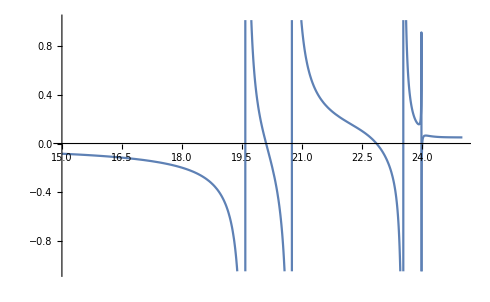

```mathematica
Plot[N[Plotter[S/.{ω->x}, 5, 1, 2]],{x, 15., 25.}, PlotRange->Automatic]
```

```mathematica
Re[mS] // MatrixForm
```

(0.793995 | 0.194249 | 0.330485 | -0.377546 | -0.229066 | 0.26832 | -0.0412268 | -0.0370778 | 0.120961 | 0.151141 | -0.0460771 | -0.0414399
-0.194249 | 0.793995 | 0.377546 | 0.330485 | -0.26832 | -0.229066 | -0.0370778 | 0.0412268 | 0.151141 | -0.120961 | -0.0414399 | 0.0460771
0.330485 | -0.377546 | 0.472178 | 0.558042 | 0.369366 | -0.421963 | 0.0718291 | 0.109147 | -0.185449 | -0.166786 | 0.0802796 | 0.121988
0.377546 | 0.330485 | -0.558042 | 0.472178 | 0.421963 | 0.369366 | 0.109147 | -0.0718291 | -0.166786 | 0.185449 | 0.121988 | -0.0802796
-0.229066 | 0.26832 | 0.369366 | -0.421963 | 0.742934 | 0.254061 | -0.0460771 | -0.0414399 | 0.135192 | 0.168922 | -0.0514979 | -0.0463152
-0.26832 | -0.229066 | 0.421963 | 0.369366 | -0.254061 | 0.742934 | -0.0414399 | 0.0460771 | 0.168922 | -0.135192 | -0.0463152 | 0.0514979
0.0412268 | -0.0370778 | -0.0718291 | 0.109147 | 0.0460771 | -0.0414399 | 1.00054 | -0.0116153 | -0.035694 | -0.125581 | 0.00236015 | -0.0756863
-0.0370778 | -0.0412268 | 0.109147 | 0.0718291 | -0.0414399 | -0.0460771 | 0.0116153 | 1.00054 | 0.125581 | -0.035694 | 0.0756863 | 0.00236015
-0.120961 | 0.151141 | 0.185449 | -0.166786 | -0.135192 | 0.168922 | -0.035694 | -0.125581 | 1.05164 | -0.0471222 | -0.0398933 | -0.140356
0.151141 | 0.120961 | -0.166786 | -0.185449 | 0.168922 | 0.135192 | 0.125581 | -0.035694 | 0.0471222 | 1.05164 | 0.140356 | -0.0398933
0.0460771 | -0.0414399 | -0.0802796 | 0.121988 | 0.0514979 | -0.0463152 | 0.00236015 | -0.0756863 | -0.0398933 | -0.140356 | 1.00106 | -0.0284866
-0.0414399 | -0.0460771 | 0.121988 | 0.0802796 | -0.0463152 | -0.0514979 | 0.0756863 | 0.00236015 | 0.140356 | -0.0398933 | 0.0284866 | 1.00106)

```mathematica
mS = S  /. {ω -> 19.81};
mSL1 = DecoupleQ[mS, n, 5];
mS1 = Re[mS.mJ.mSL1.mS];
{sympQ[mSL1], sympQ[mS1]}
Eigenvalues[mSL1.Transpose[mSL1]]
(Chop[N[mS1], 10^-8]) // MatrixForm
Scomp1=U.mS1.Inverse[U];
newM=Inverse[Id[12]-Scomp1];
Im[Chop[N[newM[[1;;6,1;;6]]],10^-8]]//MatrixForm
```

{1.,1.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

(0.48853 | 0.0535482 | 0.694208 | 0.00489482 | -0.562322 | -0.0841943 | -0.0961718 | 0.107456 | 0 | 0 | -0.107486 | 0.120098
-0.0535482 | 0.48853 | -0.00489482 | 0.694208 | 0.0841943 | -0.562322 | 0.107456 | 0.0961718 | 0 | 0 | 0.120098 | 0.107486
0.694208 | 0.00489482 | 0.0577929 | 0.00182451 | 0.77588 | 0.00547068 | 0.183019 | -0.0729661 | 0 | 0 | 0.204551 | -0.0815503
-0.00489482 | 0.694208 | -0.00182451 | 0.0577929 | -0.00547068 | 0.77588 | -0.0729661 | -0.183019 | 0 | 0 | -0.0815503 | -0.204551
-0.562322 | -0.0841943 | 0.77588 | 0.00547068 | 0.363182 | 0.0347804 | -0.107486 | 0.120098 | 0 | 0 | -0.120132 | 0.134227
0.0841943 | -0.562322 | -0.00547068 | 0.77588 | -0.0347804 | 0.363182 | 0.120098 | 0.107486 | 0 | 0 | 0.134227 | 0.120132
0.0961718 | 0.107456 | -0.183019 | -0.0729661 | 0.107486 | 0.120098 | 0.5019 | -0.895516 | 0 | 0 | -0.129692 | -0.122148
0.107456 | -0.0961718 | -0.0729661 | 0.183019 | 0.120098 | -0.107486 | 0.895516 | 0.5019 | 0 | 0 | 0.122148 | -0.129692
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0.107486 | 0.120098 | -0.204551 | -0.0815503 | 0.120132 | 0.134227 | -0.129692 | -0.122148 | 0 | 0 | 0.472991 | -0.922744
0.120098 | -0.107486 | -0.0815503 | 0.204551 | 0.134227 | -0.120132 | 0.122148 | -0.129692 | 0 | 0 | 0.922744 | 0.472991)

(53.3864 | 92.5136 | 68.3029 | 7.0128 | 0 | 7.83784
92.5136 | 148.466 | 103.398 | 11.0795 | 0 | 12.383
68.3029 | 103.398 | 68.6118 | 7.83784 | 0 | 8.75994
-7.0128 | -11.0795 | -7.83784 | -1.72268 | 0 | -0.775369
0 | 0 | 0 | 0 | 0.5 | 0
-7.83784 | -12.383 | -8.75994 | -0.775369 | 0 | -1.89552)

```mathematica
Im[N[T]] /. {ω -> 19.81} // MatrixForm
```

(21.81 | 17. | 0 | 0 | 8.5 | 0
17. | 20.81 | 19. | 8.5 | 0 | 9.5
0 | 19. | 21.81 | 0 | 9.5 | 0
0 | -8.5 | 0 | 17.81 | -17. | 0
-8.5 | 0 | -9.5 | -17. | 18.81 | -19.
0 | -9.5 | 0 | 0 | -19. | 17.81)

```mathematica
Re[N[newM[[1;;6,1;;6]]]]//MatrixForm
```

(0.5 | 4.57234×10^-12 | 3.38533×10^-12 | 3.57487×10^-13 | -2.0929×10^-14 | 4.33431×10^-13
4.27065×10^-12 | 0.5 | 5.33728×10^-12 | 5.69433×10^-13 | -3.37826×10^-14 | 6.96332×10^-13
3.01131×10^-12 | 5.07328×10^-12 | 0.5 | 3.96558×10^-13 | -2.35976×10^-14 | 4.83169×10^-13
-3.43454×10^-13 | -5.83089×10^-13 | -4.26187×10^-13 | 0.5 | 2.47436×10^-15 | -5.37348×10^-14
2.70121×10^-14 | 4.35158×10^-14 | 3.0356×10^-14 | 3.19332×10^-15 | 0.5 | 3.45956×10^-15
-4.17663×10^-13 | -7.05658×10^-13 | -5.13564×10^-13 | -5.31027×10^-14 | 2.64146×10^-15 | 0.5)